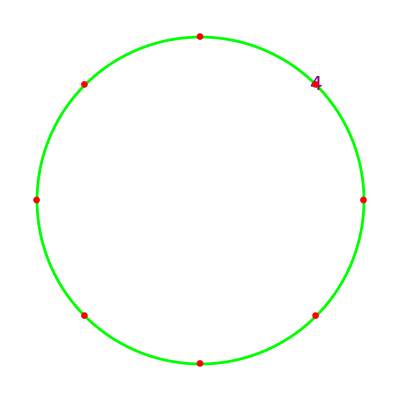

```mathematica
bits=3;
setpositenv[{bits,1}];
z:=p2x/@Range[0,2^bits-1];
c =Circle[];
p =CirclePoints[{1,-Pi/2},2^bits];
Show[Graphics[{Thickness[0.005],Green,c,PointSize[0.012],Red,Text[Style[z[[4]],Purple,20],p[[4]]],Point[p]}]]
```

```mathematica
setpositenv[{6,2}];
{nbits,es,npat,useed,minpos,maxpos,qsize,qextra}
p2x[8]
```

{6,2,64,16,1/65536,65536,128,64}

1/16

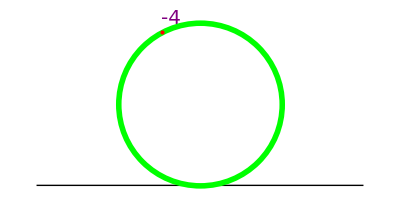

```mathematica
Show[Graphics[{Line[{{-2,0},{2,0}}],Thickness[0.01],Green,Circle[{0,1}],Red, 
Text[Style["-4",Purple,20],{-0.35,2.05}], Point[{-0.470588,1.88235}],
}]]
```